```mathematica
ClearAll["Global`*"]
```

## Defs

```mathematica
DIGITS=10;
PRECISION=40;
lastArg=1;
band=0;
period=2;
ro=10*Pi/9;
v1=0;
v2=1;
lengthBarrier=1;
lengthGap=1;
absArg=0;
```

## discontinuity matrix

```mathematica
d/:d[v1_,v2_]:=Block[
{k1=Sqrt[e-v1],k2=Sqrt[e-v2]},
da=(1+k1/k2)/2;
db=(1-k1/k2)/2;
Return[{{da,db},{db,da}}]
]
```

```mathematica
d[v1,v2]/.e->.7//MatrixForm
```

(0.5-0.763763 ⅈ | 0.5+0.763763 ⅈ
0.5+0.763763 ⅈ | 0.5-0.763763 ⅈ)

```mathematica
d[v1,v2]/.e->.7//Eigenvalues
```

{1.66533×10^-16-1.52753 ⅈ,1.-1.11022×10^-16 ⅈ}

```mathematica
Sort[d[v1,v2]/.e->.7//Eigenvalues,Abs[Abs[#1]-1]<Abs[Abs[#2]-1]&]
```

{1.-1.11022×10^-16 ⅈ,1.66533×10^-16-1.52753 ⅈ}

## propagation matrix

```mathematica
p/:p[v_,length_]:=Block[
{kl=ro*length*Sqrt[e-v]},
pa=E^(I*kl);
pb=E^(-(I*kl));
Return[{{pa,0},{0,pb}}]
]
```

```mathematica
p[v1,lengthBarrier]//MatrixForm
```

(ⅇ^(10/9 ⅈ √e π) | 0
0 | ⅇ^(-10/9 ⅈ √e π))

## TRANSFER MATRICES

```mathematica
makeTx/:makeTx[v1_,v2_,lengthBarrier_,lengthGap_]:=Block[
{tx,p1,p2,d1,d2,a,b,c},
d1=d[v1,v2];
p1=p[v2,lengthBarrier];
d2=d[v2,v1];
p2=p[v1,lengthGap];
(*tx=N[p2.d2.p1.d1,PRECISION];*)
tx=p2.d2.p1.d1;
Return[tx]]
```

```mathematica
makeTx[v1,v2,lengthBarrier,lengthGap]//MatrixForm
```

(1/4 (1-(√(-1+e))/(√e)) (1-(√e)/(√(-1+e))) ⅇ^(-10/9 ⅈ √(-1+e) π+10/9 ⅈ √e π)+1/4 (1+(√(-1+e))/(√e)) (1+(√e)/(√(-1+e))) ⅇ^(10/9 ⅈ √(-1+e) π+10/9 ⅈ √e π) | 1/4 (1-(√(-1+e))/(√e)) (1+(√e)/(√(-1+e))) ⅇ^(-10/9 ⅈ √(-1+e) π+10/9 ⅈ √e π)+1/4 (1+(√(-1+e))/(√e)) (1-(√e)/(√(-1+e))) ⅇ^(10/9 ⅈ √(-1+e) π+10/9 ⅈ √e π)
1/4 (1+(√(-1+e))/(√e)) (1-(√e)/(√(-1+e))) ⅇ^(-10/9 ⅈ √(-1+e) π-10/9 ⅈ √e π)+1/4 (1-(√(-1+e))/(√e)) (1+(√e)/(√(-1+e))) ⅇ^(10/9 ⅈ √(-1+e) π-10/9 ⅈ √e π) | 1/4 (1+(√(-1+e))/(√e)) (1+(√e)/(√(-1+e))) ⅇ^(-10/9 ⅈ √(-1+e) π-10/9 ⅈ √e π)+1/4 (1-(√(-1+e))/(√e)) (1-(√e)/(√(-1+e))) ⅇ^(10/9 ⅈ √(-1+e) π-10/9 ⅈ √e π))

```mathematica
makeUnitCell=Block[
{tx,t,i},
t=IdentityMatrix[2];
For[
i=1,
i≤period,
i++,
tx=makeTx[v1,v2,lengthBarrier,lengthGap];
v2=2+delv-v2;
t=t.tx
];
t];
```

```mathematica
(makeUnitCell/.{delv->.5,e->2})//Chop//MatrixForm
```

(-1.16796-0.0364355 ⅈ | 0.437642-0.417054 ⅈ
0.437642+0.417054 ⅈ | -1.16796+0.0364355 ⅈ)

```mathematica
(*Eigenvalues[(makeUnitCell/.{delv->0,e->0.2990799999999987})]*)
```

{0.106569-0.994305 ⅈ,0.106569+0.994305 ⅈ}

```mathematica
(*(makeUnitCell/.{delv->0,e->0.2990799999999987})*)
```

## searchBand

```mathematica
searchBand/:searchBand[start_,finish_,steps_]:=Block[
{deleov,i,zeroTol,evals,eVals,e},
plotList={};
zeroTol=1*10^(-DIGITS);
e=start;
deleov=(finish-start)/steps;
eVals=Eigenvalues[makeUnitCell];
lastArg=Arg[eVals[[1]]];
For[i=1,i≤steps+1,i++,
eVals=Eigenvalues[makeUnitCell];
evals=Abs[eVals];
If[Chop[Abs[evals[[1]]]-1,zeroTol]==0,saveArg[eVals[[1]]]];
e=e+deleov];
band=0;
]
```

```mathematica
saveArg/:saveArg[z_]:=Block[
{arg,negArg,kdoPi},
arg=Arg[z];
absArg=If[Abs[arg]-Abs[lastArg]≥ 0,absArg+(Abs[arg]-Abs[lastArg]),absArg-(Abs[arg]-Abs[lastArg])];
lastArg=arg;
kdoPi=absArg/(period*Pi);
(*Print[{makeUnitCell,kdoPi,absArg,Abs[z],arg,band,e}];*)
plotList=Append[plotList,N[{kdoPi,e},DIGITS]];]
```

```mathematica
(*saveArg/:saveArg[z_]:=Block[
{arg,negArg,kdoPi},
arg=N[Arg[z],DIGITS+1];
If[arg≥ 0,negArg=0,negArg=1];
If[Sign[lastArg]+Sign[arg]==0,band++];Print[{makeUnitCell,Abs[z],arg,band,e}];
lastArg=arg;
kdoPi=(arg+(negArg+band)*Pi)/(period*Pi);
plotList=Append[plotList,N[{kdoPi,e},DIGITS]];]*)
```

## TRANSMISSION COEFFICIENT CALCULATION

```mathematica
(*tcoeff/:tcoeff[start_,finish_,steps_,numberOfBarries_]:=Block[
{deleov,i,t22,t,e},
plotList={};
e=start;
deleov=(finish-start)/steps;
t=makeUnitCell;
t=MatrixPower[t,numberOfBarries];
t22=t[[2,2]];
For[i=1,i≤steps+1,i++,
plotList=Append[plotList,N[{e,(Abs[t22])^-2},DIGITS]];
e=e+deleov];plotList]*)
```

```mathematica
tcoeff/:tcoeff[start_,finish_,steps_,numberOfBarries_]:=Block[
{deleov,i,t22,t,e},
deleov=(finish-start)/steps;
t=MatrixPower[makeUnitCell,numberOfBarries];
plotList=Table[
t22=t[[2,2]];{e,(Abs[t22])^-2}/.e->evalue,{evalue,start,finish, deleov}];
]
```

## Figs

```mathematica
plotList={};fig2[delv0_,st_,fin_,stp_]:=Block[
{
delv=delv0
},
absArg=0;
searchBand[st,fin,stp];
ListPlot[plotList,
AxesLabel->{"kd/π","E/V"},
PlotLabel->Row[{"delv = ",delv}
]
]
]
```

```mathematica
fig4[delv0_,st_,fin_,stp_,nob_]:=Block[
{
delv=delv0
},
absArg=0;
tcoeff[st,fin,stp,nob];
ListPlot[plotList,
Joined->True,
AxesLabel->{"E/V","T"},
PlotLabel->Row[{"Number of barriers = ",nob}],
PlotRange->All
]
]
```

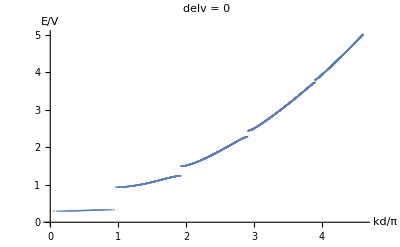

```mathematica
fig2[0,0.01,5,10000]
```

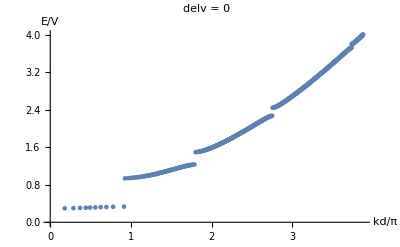
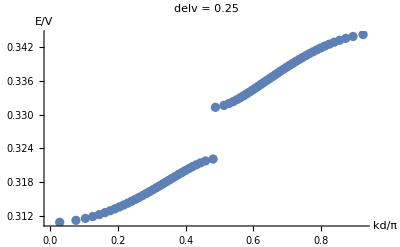
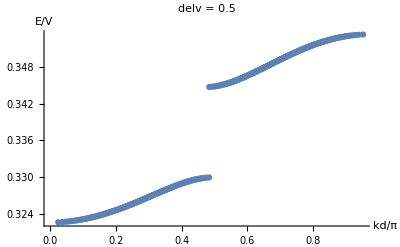

```mathematica
{fig2[0,0.01,4,1000],fig2[0.25,0.01,.35,1000],fig2[0.5,0.01,.4,10000]}
```

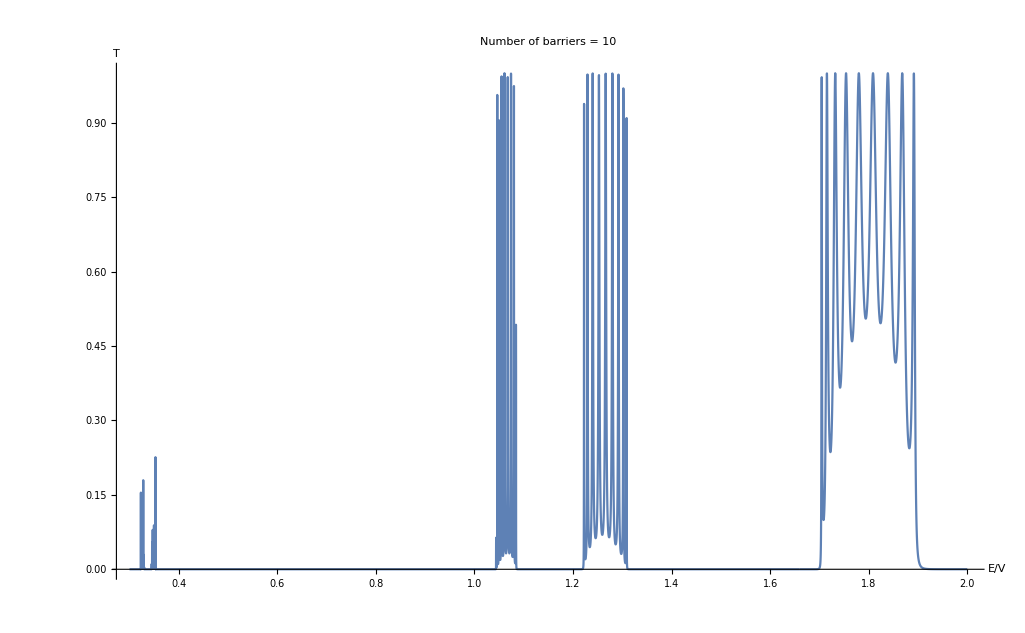

```mathematica
fig4[0.5,.3,2,10000,10]
```